```mathematica
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]


MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
```

```mathematica
SetDirectory["/Users/4/Documents/Weak interactions/tank data"];
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
For[i=18,i≤33,i++,
prodata[i] = ProcessData[rawdata[i],1];
m[i]=MAR[prodata[i],1,{}]
]
```

```mathematica
(*Find distribution of B matrices (for off-diagonal and on-diagonal) and produce some new B matrices to use as "known" B matrices*)
(*Find covariance matrix of Sigma for the data and use that to produce noise*)
(*Refer to picture on your phone*)
(*Actual data took 26 samples from 6 tanks*)
(*Standard deviation for estimated B matrix should be smaller than known B matrix and tests for stability should be the similar if good estimate*)
```

```mathematica
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]
GenPreBNew[p_]:=Module[{botEd,botIned,topEd,topIned,algaeDiag,speciesDiag,algaeComp,speciesComp,B,b,i,j},
botEd=RandomVariate[NormalDistribution[-0.167,0.225],p-2];
botIned=RandomVariate[NormalDistribution[-0.162,0.224],p-2];
topEd=RandomVariate[NormalDistribution[-0.162,0.224],p-2];
topIned=RandomVariate[NormalDistribution[-0.159,0.227],p-2];
algaeDiag=RandomVariate[NormalDistribution[0.509,0.224],2];
speciesDiag=RandomVariate[NormalDistribution[0.658,0.132],p-2];
algaeComp=RandomVariate[NormalDistribution[0.092,0.232],2];
If[p>3,
speciesComp=RandomVariate[NormalDistribution[-0.056,0.131],{p-2,p-2}];
];
B=Table[0,{q,1,p},{r,1,p}];

For[i=1,i≤p-2,i++,
B[[i,i]]=speciesDiag[[i]];
For[j=1,j≤p-2,j++,
If[i≠j,
B[[i,j]]=speciesComp[[i,j]];
];
];
];

i=p-1;
For[j=1,j≤p-2,j++,
B[[i,j]]=botEd[[j]];
B[[i+1,j]]=botIned[[j]];
B[[j,i]]=topEd[[j]];
B[[j,i+1]]=topIned[[j]];
];

B[[p-1,p-1]]=algaeDiag[[1]];
B[[p,p]]=algaeDiag[[2]];
B[[p-1,p]]=algaeComp[[1]];
B[[p,p-1]]=algaeComp[[2]];

B
]
GenBNew[p_]:=Module[{B},
B=GenPreBNew[p];
While[Max[Abs[Eigenvalues[B]]]≥1,B=GenPreBNew[p]];
B
]
GenPreSigma[p_]:=Module[{diags,preSig,Sig,b,i},
diags=DiagonalMatrix[RandomVariate[NormalDistribution[3.22144,1.97698],p]/2];
preSig=UpperTriangularize[RandomVariate[NormalDistribution[0.479896,0.98371],{p,p}],1]; (* Generates the upper triangular part of the Sigma matrix which will be transposed and added to give a symmetic matrix *)
Sig=diags+preSig;
Sig=Sig+Transpose[Sig]
]
(* Generate Sigma matrices until an acceptable Sigma matrix is produced *)
GenSigma[p_]:=Module[{Sig},
Sig=GenPreSigma[p];
While[Not[PositiveSemidefiniteMatrixQ[Sig]],Sig=GenPreSigma[p]];
Sig
]
```

```mathematica
For[i=1,i≤17,i++,
p=Length[m[i]];
cov=Length[m[i][[1]]]-p-1;
Amatrix[i] = m[i][[All,1;;1]];
Bmatrix[i] = B[m[i]];
If[cov == 0,
Cmatrix[i] = 0,
Cmatrix[i] = m[i][[All,2;;2+cov-1]]]
]
prodata[1][[1]]
```

{{-3.7966,4.2223,2.33311},{-3.7966,4.67227,-5.29832},{-3.7966,5.59827,3.31273},{-3.7966,4.61542,1.14422},{-0.890054,4.5743,2.7447},{-0.786299,4.65053,1.43031},{-3.7966,4.4666,2.14593},{-0.786299,4.4666,2.14593},{-3.7966,3.00618,0.524729},{-3.7966,3.26995,1.10856},{-3.7966,3.11928,2.1883},{0.523206,3.35446,1.19089},{1.08662,2.99423,2.42392},{1.29314,3.00964,0.722706},{1.40771,3.4128,-5.29832},{2.14771,3.59759,0.392042},{1.64808,4.0189,1.71019},{2.8311,3.95623,2.26696},{0.716171,3.99434,1.81156},{-3.7966,3.91681,1.51513},{-3.7966,3.77826,0.139762},{-0.196907,3.89304,3.13157},{-1.71716,3.55506,0.8671},{-3.10345,3.23514,0.0953102},{-3.7966,5.28973,3.8582},{-2.00484,3.25771,-1.89712}}

```mathematica
For[i=1,i≤17,i++,
noise[i] = {};
For[j=1,j≤Length[prodata[i]],j++,
noiseprep1[j]={};
noiseprep2[j]={};
For[k=1,k≤Length[prodata[i][[j]]]-1,k++,
noiseprep1[j] = Join[noiseprep1[j],{prodata[i][[j,k+1]]-Amatrix[i]-Bmatrix[i].prodata[i][[j,k]]}];
noiseprep2[j] = Join[noiseprep2[j],Transpose[noiseprep1[j][[k]]]]
];
noise[i] =Join[noise[i],{noiseprep2[j]}]
];
covar[i]={};
For[j=1,j≤Length[noise[i]],j++,
covar[i]=Join[covar[i],{Covariance[noise[i][[j]]]}]
]
]
covar[1]
```

{{{3.41615,-0.00477982,0.290084},{-0.00477982,0.401376,0.421965},{0.290084,0.421965,5.28084}},{{3.76481,-0.194817,-0.0538784},{-0.194817,1.35703,1.01786},{-0.0538784,1.01786,1.72787}},{{8.35667,0.101928,-0.260362},{0.101928,0.807912,0.54894},{-0.260362,0.54894,0.91344}},{{4.46718,-0.593411,-0.824836},{-0.593411,1.15659,-0.0730475},{-0.824836,-0.0730475,5.43734}},{{7.14908,0.518367,3.35394},{0.518367,1.37325,1.70133},{3.35394,1.70133,6.34407}},{{6.99683,0.564151,0.486896},{0.564151,0.659561,0.521248},{0.486896,0.521248,1.25276}}}

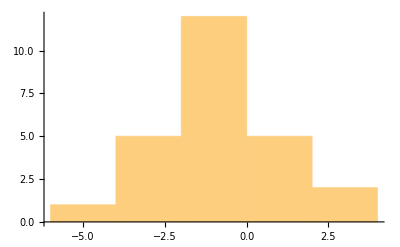

1.84828

```mathematica
Histogram[noise[1][[1,All,1]]]
StandardDeviation[noise[1][[1,All,1]]]
```

```mathematica
(*Using all B matrices*)
odlist = {};
dlist={};
For[i=1,i≤17,i++,
For[j=1,j≤Length[Bmatrix[i]],j++,
For[k=1,k≤Length[Bmatrix[i][[j]]],k++,
If[j≠k,
odlist = Join[odlist,{Bmatrix[i][[j,k]]}],
dlist = Join[dlist,{Bmatrix[i][[j,k]]}]
]
]
]
]
```

```mathematica
(*Using one Bmatrix*)
odlist={};
dlist={};
For[i=1,i≤Length[Bmatrix[1]],i++,
For[j=1,j≤Length[Bmatrix[1][[i]]],j++,
If[i==j,
dlist = Join[dlist,{Bmatrix[1][[i,j]]}],
odlist = Join[odlist,{Bmatrix[1][[i,j]]}]
]
]
]
```

```mathematica
(*Use this*)
numB = 100;
nump = 2;
For[i=1,i≤numB,i++,
TestB[i]=GenBNew[nump];
Sigma[i]=GenSigma[nump];
]
```

```mathematica
numB = 100;
For[i=1,i≤numB,i++,
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
If[j≠k,
Bmat[j,k]=RandomVariate[NormalDistribution[Mean[odlist],StandardDeviation[odlist]]],
Bmat[j,k]=RandomVariate[NormalDistribution[Mean[odlist],StandardDeviation[dlist]]]
]
]
];
TestB[i] = Array[Bmat,{3,3}]
]
(*For[i=1,i≤117,i++,
If[i≤17,
allB[i] = Bmatrix[i],
allB[i] = TestB[i-17]
]
]*)
```

```mathematica
distlist={};
For[i=1,i≤ Length[prodata[1]],i++,
distlist=Join[distlist,prodata[1][[i,1]]]
]
```

```mathematica
(*Only uses B matrices that were produced from the statistical properties of the B matrices from the data*)
maxt = 10;
iter = 50;
For[i=1,i≤numB,i++,
Bmatrix2[i] = {};
For[j=1,j≤ iter,j++,
Et[i] =RandomVariate[MultinormalDistribution[Sigma[i]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = RandomVariate[NormalDistribution[Mean[distlist],StandardDeviation[distlist]],{nump,1}];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
]
]
```

```mathematica
For[i=1,i≤numB,i++,
oldodlist[i] = {};
olddlist[i] = {};
newodlist[i] = {};
newdlist[i] = {};
For[k=1,k≤nump,k++,
For[l=1,l≤nump,l++,
If[k≠l,
oldodlist[i]=Join[oldodlist[i],{TestB[i][[k,l]]}],
olddlist[i]=Join[olddlist[i],{TestB[i][[k,l]]}];
]
]
];
For[j=1,j≤iter,j++,
For[k=1,k≤nump,k++,
For[l=1,l≤nump,l++,
If[k≠l,
newodlist[i]=Join[newodlist[i],{Bmatrix2[i][[j,k,l]]}],
newdlist[i] = Join[newdlist[i],{Bmatrix2[i][[j,k,l]]}]
]
]
]
];
stdodold[i] = StandardDeviation[oldodlist[i]];
stddold[i]=StandardDeviation[olddlist[i]];
(*stdodknown[i] = StandardDeviation[odlist];
stddknown[i] = StandardDeviation[dlist];*)
stdodest[i] = StandardDeviation[newodlist[i]];
stddest[i] = StandardDeviation[newdlist[i]];
];
```

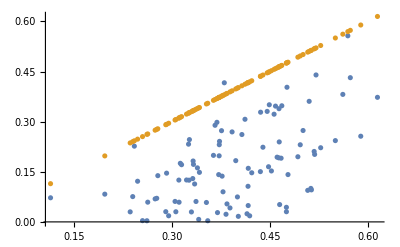

```mathematica
(*DiscretePlot[{stddest[x],stddold[x]},{x,1,numB}]*)
complist={};
linelist={};
For[i=1,i≤numB,i++,
complist=Join[complist,{{stdodest[i],stdodold[i]}}];
linelist=Join[linelist,{{stdodest[i],stdodest[i]}}]
]
ListPlot[{complist,linelist}]
(*Blue is for estimated B matrices, yellow is for "known" B matrices*)
```

```mathematica
For[i=1,i≤numB,i++,
eiglist[i] = {};
maxeig[i]={};
geomean[i] = {};
For[j=1,j≤iter,j++,
eiglist[i] = Join[eiglist[i],{Eigenvalues[Bmatrix2[i][[j]]]}];
maxeig[i]=Join[maxeig[i],{Max[Re[eiglist[i][[j]]]]}];
geomean[i]=Join[geomean[i],{Abs[GeometricMean[eiglist[i][[j]]]]}]
]
]
```

```mathematica
plotlist = {};
For[i=1,i≤numB,i++,
If[Im[Mean[geomean[i]]]==0,
plotlist=Join[plotlist,{{Mean[maxeig[i]],Mean[geomean[i]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
(*x-axis is maximum eigenvalue, y-axis is geometric mean of eigenvalues*)
```

```mathematica
plotlist = {};

For[j=1,j≤iter,j++,
If[Im[geomean[25][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[25][[j]],Re[geomean[25][[j]]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
```

```mathematica
maxr=0;
For[i=1,i≤numB,i++,
plotlist={};
For[j=1,j≤iter,j++,
If[Im[geomean[i][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[i][[j]],Re[geomean[i][[j]]]}}]
]
];
If[plotlist=={},
rsq[i] = 0,
rsq[i]=LinearModelFit[plotlist,x,x]["RSquared"]
]
If[maxr<rsq[i],
maxr=rsq[i];
trueplotlist=plotlist
]
]
ListPlot[trueplotlist]
```

```mathematica
Bmatrix2[1] = {};
iter=200;
maxt=50;
For[j=1,j≤ iter,j++,
Et[1] =RandomVariate[MultinormalDistribution[covar[1][[1]]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = Amatrix[1]+Bmatrix[1].X[l-1]+Transpose[{Et[1][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[1]=Join[Bmatrix2[1],{prep3}]
]
```

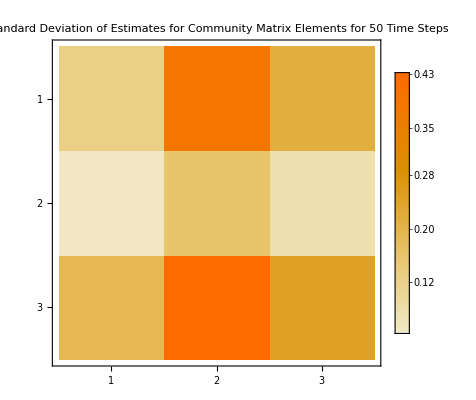

```mathematica
For[i=1,i≤iter,i++,
For[j=1,j≤Length[Bmatrix2[1][[i]]],j++,
For[k=1,k≤Length[Bmatrix2[1][[i,j]]],k++,
If[i==1,
stdprep[j,k]={}
];
stdprep[j,k]=Join[stdprep[j,k],{Bmatrix2[1][[i,j,k]]}]
]
];
]
For[l=1,l≤iter,l++,
For[m=1,m≤Length[Bmatrix2[1][[l]]],m++,
For[n=1,n≤Length[Bmatrix2[1][[l,m]]],n++,
stdfunc[m,n]=StandardDeviation[stdprep[m,n]];
meanfunc[m,n]=Mean[stdprep[m,n]]
]
]
]
stdarray=Array[stdfunc,{3,3}];
meanarray=Array[meanfunc,{3,3}];
MatrixPlot[stdarray,PlotLegends->Automatic,PlotLabel->"Standard Deviation of Estimates for Community Matrix Elements \n for 50 Time Steps"]
```

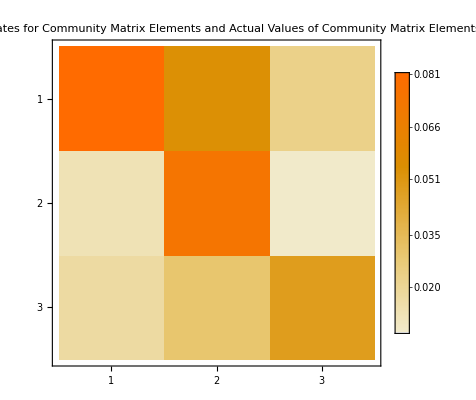

```mathematica
MatrixPlot[Abs[Bmatrix[1]-meanarray],PlotLegends->Automatic,PlotLabel->"Difference Between Estimates for Community Matrix Elements \n and Actual Values of Community Matrix Elements \n for 50 Time Steps"]
```

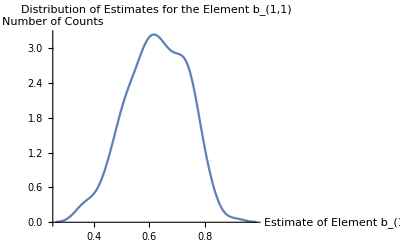

0.626456

0.707983

```mathematica
SmoothHistogram[stdprep[1,1],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,1,1], AxesLabel->{"Estimate of Element "Subscript[b,1,1],"Number of Counts"}]
meanarray[[1,1]]
Bmatrix[1][[1,1]]
```

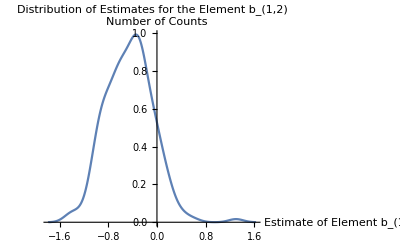

-0.451906

-0.407981

```mathematica
SmoothHistogram[stdprep[1,2],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,1,2], AxesLabel->{"Estimate of Element "Subscript[b,1,2],"Number of Counts"}]
meanarray[[1,2]]
Bmatrix[1][[1,2]]
```

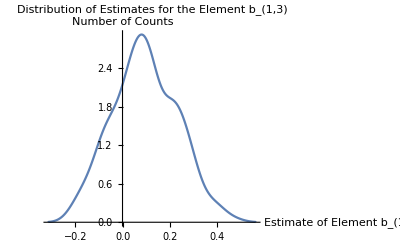

0.0947144

0.0861775

```mathematica
SmoothHistogram[stdprep[1,3],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,1,3], AxesLabel->{"Estimate of Element "Subscript[b,1,3],"Number of Counts"}]
meanarray[[1,3]]
Bmatrix[1][[1,3]]
```

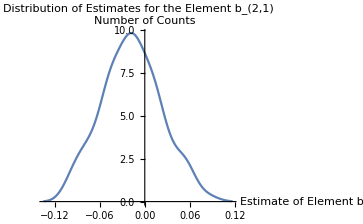

-0.0176136

-0.0227186

```mathematica
SmoothHistogram[stdprep[2,1],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,2,1], AxesLabel->{"Estimate of Element "Subscript[b,2,1],"Number of Counts"}]
meanarray[[2,1]]
Bmatrix[1][[2,1]]
```

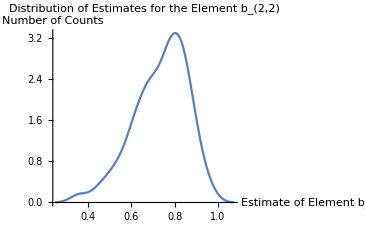

0.734915

0.80994

```mathematica
SmoothHistogram[stdprep[2,2],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,2,2], AxesLabel->{"Estimate of Element "Subscript[b,2,2],"Number of Counts"}]
meanarray[[2,2]]
Bmatrix[1][[2,2]]
```

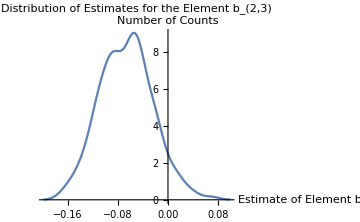

-0.0669075

-0.0627321

```mathematica
SmoothHistogram[stdprep[2,3],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,2,3], AxesLabel->{"Estimate of Element "Subscript[b,2,3],"Number of Counts"}]
meanarray[[2,3]]
Bmatrix[1][[2,3]]
```

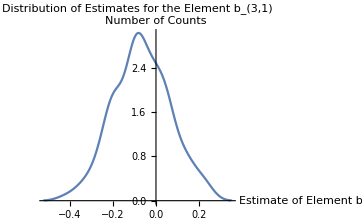

-0.0667777

-0.061149

```mathematica
SmoothHistogram[stdprep[3,1],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,3,1], AxesLabel->{"Estimate of Element "Subscript[b,3,1],"Number of Counts"}]
meanarray[[3,1]]
Bmatrix[1][[3,1]]
```

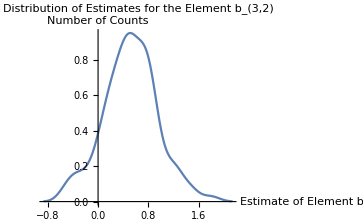

0.518716

0.506034

```mathematica
SmoothHistogram[stdprep[3,2],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,3,2], AxesLabel->{"Estimate of Element "Subscript[b,3,2],"Number of Counts"}]
meanarray[[3,2]]
Bmatrix[1][[3,2]]
```

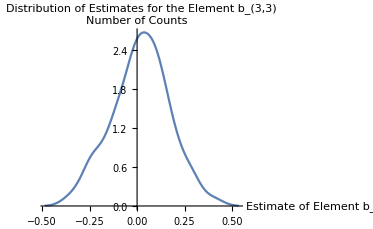

0.0193228

0.060775

```mathematica
SmoothHistogram[stdprep[3,3],PlotLabel->"Distribution of Estimates for the Element " Subscript[b,3,3], AxesLabel->{"Estimate of Element "Subscript[b,3,3],"Number of Counts"}]
meanarray[[3,3]]
Bmatrix[1][[3,3]]
```

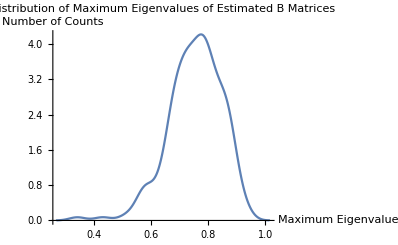

0.753686

0.820138

```mathematica
maxeiglist={};
For[i=1,i≤Length[Bmatrix2[1]],i++,
maxeiglist=Join[maxeiglist,{Max[Abs[Eigenvalues[Bmatrix2[1][[i]]]]]}]
]
SmoothHistogram[maxeiglist,PlotLabel-> "Distribution of Maximum Eigenvalues of Estimated B Matrices",AxesLabel->{"Maximum Eigenvalue","Number of Counts"}]
Mean[maxeiglist]
Max[Abs[Eigenvalues[Bmatrix[1]]]]
```

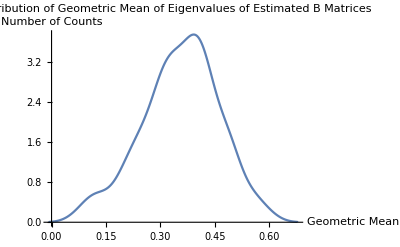

0.354709

0.388138

```mathematica
geomeanlist={};
For[i=1,i≤Length[Bmatrix2[1]],i++,
geomeanlist=Join[geomeanlist,{Abs[GeometricMean[Eigenvalues[Bmatrix2[1][[i]]]]]}]
]
SmoothHistogram[geomeanlist,PlotLabel-> "Distribution of Geometric Mean of Eigenvalues of Estimated B Matrices",AxesLabel->{"Geometric Mean","Number of Counts"}]
Mean[geomeanlist]
Abs[GeometricMean[Eigenvalues[Bmatrix[1]]]]
```

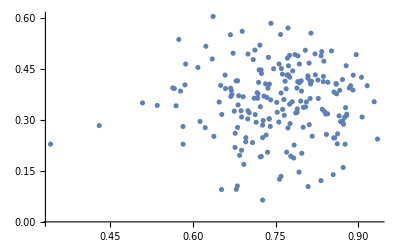

```mathematica
totlist={};
For[i=1,i≤Length[maxeiglist],i++,
totlist=Join[totlist,{{maxeiglist[[i]],geomeanlist[[i]]}}]
]
ListPlot[totlist]
```

```mathematica
For[i=2,i≤10000,i++,
Bmatrix2[i] = {};
iter=200;
maxt=i;
For[j=1,j≤ iter,j++,
Et[1] =RandomVariate[MultinormalDistribution[covar[1][[1]]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = Amatrix[1]+Bmatrix[1].X[l-1]+Transpose[{Et[1][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
];
For[j=1,j≤iter,j++,
For[k=1,k≤Length[Bmatrix2[i][[j]]],k++,
For[l=1,l≤Length[Bmatrix2[i][[j,k]]],l++,
If[j==1,
stdprep[k,l]={}
];
stdprep[k,l]=Join[stdprep[k,l],{Bmatrix2[i][[j,k,l]]}]
]
];
];
For[l=1,l≤iter,l++,
For[m=1,m≤Length[Bmatrix2[i][[l]]],m++,
For[n=1,n≤Length[Bmatrix2[i][[l,m]]],n++,
stdfunc[m,n]=StandardDeviation[stdprep[m,n]];
meanfunc[m,n]=Mean[stdprep[m,n]]
]
]
];
stdarray1[i]=Array[stdfunc,{3,3}];
meanarray1[i]=Array[meanfunc,{3,3}];
]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.,2.00532,14.5884,-5.40802},{2.00532,1.68499,3.29865,-2.38913},{14.5884,3.29865,38.4808,-11.3789},{-5.40802,-2.38913,-11.3789,6.54819}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

$Aborted

```mathematica
For[i=2,i≤10000,i++,
maxstd[i] = 0;
minstd[i]=1000000000000;
maxdif[i]=0;
mindif[i]=1000000000000;
avgstd[i] = 0;
avgdif[i] = 0;
phold=0;
totalstd = 0;
totaldif = 0;
For[j=1,j≤Length[stdarray1[i]],j++,
For[k=1,k≤Length[stdarray1[i][[j]]],k++,
phold=stdarray1[i][[j,k]];
totalstd=totalstd + phold;
If[phold>maxstd[i],
maxstd[i]=phold
];
If[phold<minstd[i],
minstd[i]=phold
];
phold=Abs[Bmatrix[1][[j,k]]-meanarray1[i][[j,k]]];
totaldif=totaldif+phold;
If[phold>maxdif[i],
maxdif[i]=phold
];
If[phold<mindif[i],
mindif[i]=phold
]
]
];
avgstd[i]=totalstd/Length[stdarray1[i]]^2;
avgdif[i]=totaldif/Length[meanarray1[i]]^2
]
```

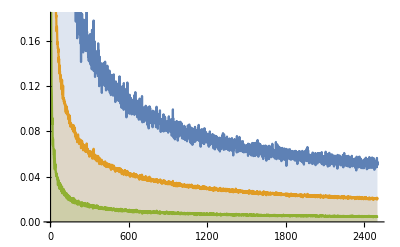

```mathematica
DiscretePlot[{maxstd[x],avgstd[x],minstd[x]},{x,2,2500}]
```

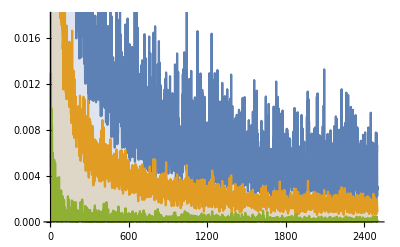

```mathematica
DiscretePlot[{maxdif[x],avgdif[x],mindif[x]},{x,2,2500}]
```

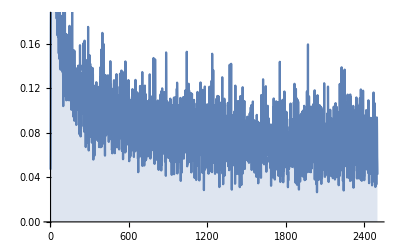

```mathematica
DiscretePlot[avgdif[x]/avgstd[x],{x,2,2500}]
```

```mathematica
mindif[2]
```

0.137072

```mathematica
numB=100;
(*For[a=2,a≤6,a++,*)
nump = 6;
goodest[nump]=0;
(*For[b=2,goodest[a]≤0.5*iter,b++,*)
goodest[nump]=0;
For[i=1,i≤numB,i++,
TestB[i]=GenBNew[nump];
Sigma[i]=GenSigma[nump];
];
distlist={};
For[i=1,i≤ Length[prodata[1]],i++,
distlist=Join[distlist,prodata[1][[i,1]]]
];
maxt = 50;
iter = 50;
For[i=1,i≤numB,i++,
Bmatrix2[i] = {};
For[j=1,j≤ iter,j++,
Et[i] =RandomVariate[MultinormalDistribution[Sigma[i]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = RandomVariate[NormalDistribution[Mean[distlist],StandardDeviation[distlist]],{nump,1}];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
]
];
For[i=1,i≤iter,i++,
For[j=1,j≤Length[Bmatrix2[1][[i]]],j++,
For[k=1,k≤Length[Bmatrix2[1][[i,j]]],k++,
If[i==1,
stdprep[j,k]={}
];
stdprep[j,k]=Join[stdprep[j,k],{Bmatrix2[1][[i,j,k]]}]
]
];
];
For[i=1,i≤numB,i++,
For[j=1,j≤Length[TestB[i]],j++,
For[k=1,k≤Length[TestB[i][[j]]],k++,
If[i==1,
stdprepold[j,k]={}
];
stdprepold[j,k]=Join[stdprepold[j,k],{TestB[i][[j,k]]}]
]
]
];
For[l=1,l≤numB,l++,
For[n=1,n≤Length[TestB[l]],n++,
For[o=1,o≤Length[TestB[l][[n]]],o++,
stdfuncold[n,o]=StandardDeviation[stdprepold[n,o]]
]
]
];
For[l=1,l≤iter,l++,
For[n=1,n≤Length[Bmatrix2[1][[l]]],n++,
For[o=1,o≤Length[Bmatrix2[1][[l,n]]],o++,
stdfunc[n,o]=StandardDeviation[stdprep[n,o]];
]
];
stdarray[l]=Array[stdfunc,{nump,nump}];
stdarrayold[a]=Array[stdfuncold,{nump,nump}];
comparray[l]=stdarrayold[a]-stdarray[l];
If[Mean[Mean[comparray[l]]]>0,
goodest[nump]=goodest[nump]+1
]
]

numtim[a]=b
```

8

```mathematica
nump
goodest[nump]
```

6

50

```mathematica
a
```

2

```mathematica
(*Theor. stab. vs epir. stab*)
(*coeficient of variation*)
(* weighted average CV*)
```

0.0848442

0.0848442

```mathematica
maxt = 50;
iter = 50;
nump=5;
numB=10000;
For[i=1,i≤numB,i++,
TestB[i]=GenBNew[nump];
Sigma[i]=GenSigma[nump];
];
For[i=1,i≤numB,i++,
expXbiglist[i]={};
For[j=1,j≤ iter,j++,
Et[i] =RandomVariate[MultinormalDistribution[Sigma[i]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = RandomVariate[NormalDistribution[Mean[distlist],StandardDeviation[distlist]],{nump,1}];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[n=1,n≤Length[X[l]],n++,
prep1 = Join[prep1,X[l][[n]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
expXlist[j]=Exp[Xlist[j]];
expXbiglist[i]=Join[expXbiglist[i],{expXlist[j]}];
]
]
```

```mathematica
For[i=1,i≤numB,i++,
Beigenmax[i]=Max[Abs[Eigenvalues[TestB[i]]]];
Bgeomean[i]=Abs[GeometricMean[Eigenvalues[TestB[i]]]];
For[j=1,j≤iter,j++,
For[k=1,k≤Length[expXbiglist[i][[j]]],k++, (*for now, this is length of prodata[1]*)
expXmean[i,j,k]=Mean[expXbiglist[i][[j,k]]];
expXstd[i,j,k]=StandardDeviation[expXbiglist[i][[j,k]]];
expXtotal[i,j,k]={};
For[l=1,l≤maxt,l++,
expXtotal[i,j,k]=Join[expXtotal[i,j,k],{Total[expXbiglist[i][[j,k,l]]]}]
];
PCV[i,j,k]=Total[expXstd[i,j,k]/expXmean[i,j,k]]/nump;
WPCV[i,j,k]=Total[expXstd[i,j,k]]/Total[expXmean[i,j,k]];
CCV[i,j,k]=StandardDeviation[expXtotal[i,j,k]]/Mean[expXtotal[i,j,k]]
]
]
]
PCVarray=Array[PCV,{numB,iter,Length[prodata[1]]}];
WPCVarray=Array[WPCV,{numB,iter,Length[prodata[1]]}];
CCVarray=Array[CCV,{numB,iter,Length[prodata[1]]}];
Beigenmaxarray=Array[Beigenmax,numB];
Bgeomeanarray=Array[Bgeomean,numB];
```

```mathematica
PCVME={};
PCVGM={};
WPCVME={};
WPCVGM={};
CCVME={};
CCVGM={};
For[i=1,i≤numB,i++,
PCVME=Join[PCVME,{{Mean[Mean[PCVarray[[i]]]],Beigenmaxarray[[i]]}}];
PCVGM=Join[PCVGM,{{Mean[Mean[PCVarray[[i]]]],Bgeomeanarray[[i]]}}];
WPCVME=Join[WPCVME,{{Mean[Mean[WPCVarray[[i]]]],Beigenmaxarray[[i]]}}];
WPCVGM=Join[WPCVGM,{{Mean[Mean[WPCVarray[[i]]]],Bgeomeanarray[[i]]}}];
CCVME=Join[CCVME,{{Mean[Mean[CCVarray[[i]]]],Beigenmaxarray[[i]]}}];
CCVGM=Join[CCVGM,{{Mean[Mean[CCVarray[[i]]]],Bgeomeanarray[[i]]}}]
]

MEPCV={};
GMPCV={};
MEWPCV={};
GMWPCV={};
MECCV={};
GMCCV={};
For[i=1,i≤numB,i++,
MEPCV=Join[MEPCV,{{Beigenmaxarray[[i]],Mean[Mean[PCVarray[[i]]]]}}];
GMPCV=Join[GMPCV,{{Bgeomeanarray[[i]],Mean[Mean[PCVarray[[i]]]]}}];
MEWPCV=Join[MEPCV,{{Beigenmaxarray[[i]],Mean[Mean[WPCVarray[[i]]]]}}];
GMWPCV=Join[GMWPCV,{{Bgeomeanarray[[i]],Mean[Mean[WPCVarray[[i]]]]}}];
MECCV=Join[MECCV,{{Beigenmaxarray[[i]],Mean[Mean[CCVarray[[i]]]]}}];
GMCCV=Join[GMCCV,{{Bgeomeanarray[[i]],Mean[Mean[CCVarray[[i]]]]}}]
]
```

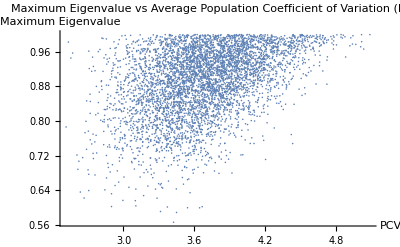

0.172475

```mathematica
ListPlot[PCVME,PlotLabel->"Maximum Eigenvalue vs Average Population \n Coefficient of Variation (PCV)",AxesLabel->{"PCV","Maximum Eigenvalue"}]
LinearModelFit[PCVME,x,x]["RSquared"]
```

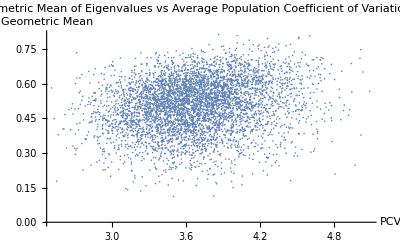

0.0410388

```mathematica
ListPlot[PCVGM,PlotLabel->"Geometric Mean of Eigenvalues vs Average Population \n Coefficient of Variation (PCV)",AxesLabel->{"PCV","Geometric Mean"}]
LinearModelFit[PCVGM,x,x]["RSquared"]
```

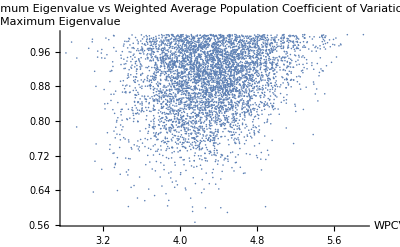

0.0403565

```mathematica
ListPlot[WPCVME,PlotLabel->"Maximum Eigenvalue vs Weighted Average \n Population Coefficient of Variation (WPCV)",AxesLabel->{"WPCV","Maximum Eigenvalue"}]
LinearModelFit[WPCVME,x,x]["RSquared"]
```

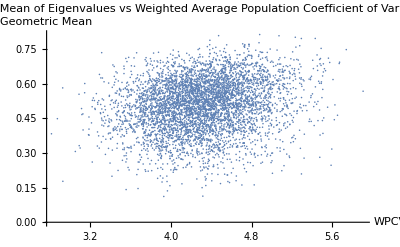

0.0360718

```mathematica
ListPlot[WPCVGM,PlotLabel->"Geometric Mean of Eigenvalues vs Weighted Average \n Population Coefficient of Variation (WPCV)",AxesLabel->{"WPCV","Geometric Mean"}]
LinearModelFit[WPCVGM,x,x]["RSquared"]
```

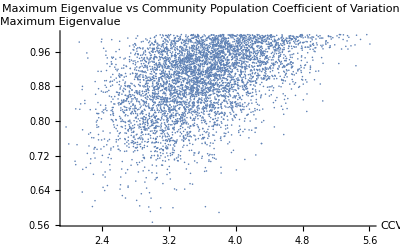

0.207783

```mathematica
ListPlot[CCVME,PlotLabel->"Maximum Eigenvalue vs Community Population \n Coefficient of Variation (CCV)",AxesLabel->{"CCV","Maximum Eigenvalue"}]
LinearModelFit[CCVME,x,x]["RSquared"]
```

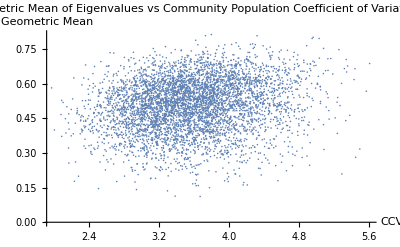

0.0314201

```mathematica
ListPlot[CCVGM,PlotLabel->"Geometric Mean of Eigenvalues vs Community Population \n Coefficient of Variation (CCV)",AxesLabel->{"CCV","Geometric Mean"}]
LinearModelFit[CCVGM,x,x]["RSquared"]
```

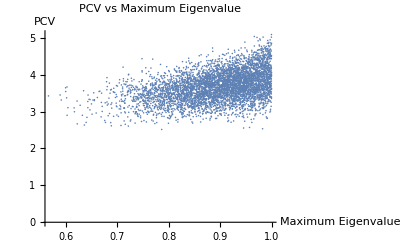

0.172475

```mathematica
ListPlot[MEPCV,PlotLabel->"PCV vs Maximum Eigenvalue",AxesLabel->{"Maximum Eigenvalue","PCV"}]
LinearModelFit[MEPCV,x,x]["RSquared"]
```

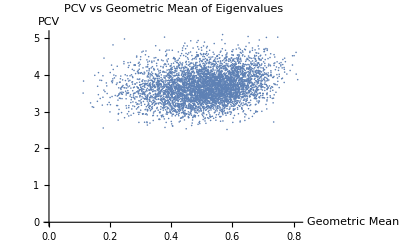

0.0410388

```mathematica
ListPlot[GMPCV,PlotLabel->"PCV vs Geometric Mean of Eigenvalues",AxesLabel->{"Geometric Mean","PCV"}]
LinearModelFit[GMPCV,x,x]["RSquared"]
```

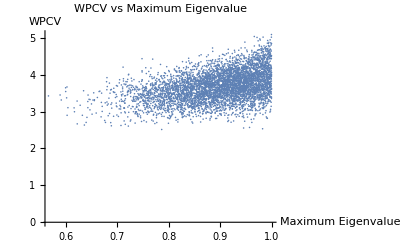

0.172442

```mathematica
ListPlot[MEWPCV,PlotLabel->"WPCV vs Maximum Eigenvalue",AxesLabel->{"Maximum Eigenvalue","WPCV"}]
LinearModelFit[MEWPCV,x,x]["RSquared"]
```

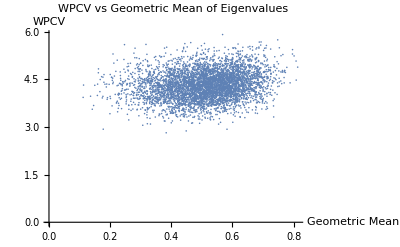

0.0410388

```mathematica
ListPlot[GMWPCV,PlotLabel->"WPCV vs Geometric Mean of Eigenvalues",AxesLabel->{"Geometric Mean","WPCV"}]
LinearModelFit[GMPCV,x,x]["RSquared"]
```

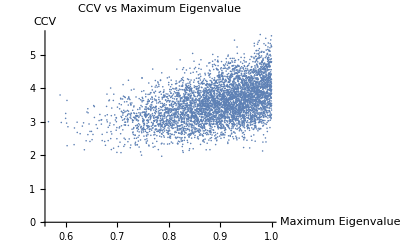

0.207783

```mathematica
ListPlot[MECCV,PlotLabel->"CCV vs Maximum Eigenvalue",AxesLabel->{"Maximum Eigenvalue","CCV"}]
LinearModelFit[MECCV,x,x]["RSquared"]
```

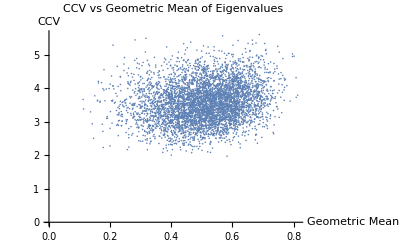

0.0314201

```mathematica
ListPlot[GMCCV,PlotLabel->"CCV vs Geometric Mean of Eigenvalues",AxesLabel->{"Geometric Mean","CCV"}]
LinearModelFit[GMCCV,x,x]["RSquared"]
```